```mathematica
ClearAll["Global`*"]
```

## Se82

```mathematica
enBMSe={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
strBMSe={0.0000000312,0.0000001089,0.0000003604,0.0000011282,0.0000033407,0.0000093590,0.0000248047,0.0000621953,0.0001475364,0.0003310990,0.0007029659,0.0014119791,0.0026831186,0.0048235755,0.0082038155,0.0132001935,0.0200938113,0.0289375648,0.0394256935,0.0508176496,0.0619680957,0.0714893508,0.0780257037,0.0805687746,0.0787144966,0.0727734636,0.0636966549,0.0528464378,0.0416968591,0.0315633168,0.0234353628,0.0179337921,0.0153606553,0.0157809819,0.0190772605,0.0249469899,0.0328546825,0.0419839605,0.0512472424,0.0593930554,0.0652097702,0.0677772776,0.0666881937,0.0621653916,0.0550448434,0.0466551429,0.0386796753,0.0331082248,0.0323588056,0.0395810317,0.0590567421,0.0965202634,0.1591678434,0.2551559423,0.3925284670,0.5777428544,0.8141908163,1.1011858520,1.4337023424,1.8027320564,2.1957054818,2.5963463286,2.9837964422,3.3317095220,3.6087251824,3.7816711172,3.8217502685,3.7122795759,3.4552084809,3.0735584482,2.6083175509,2.1105453430,1.6313385804,1.2129262995,0.8833030404,0.6550678053,0.5274768227,0.4898976171,0.5250652935,0.6114345502,0.7248766863,0.8404663762,0.9349460899,0.9898291191,0.9944245366,0.9477563240,0.8585952129,0.7434938294,0.6234447121,0.5201802915,0.4530232963,0.4366944548,0.4799254176,0.5844515425,0.7441232757,0.9443505406,1.1625480381,1.3703261289,1.5377074241,1.6387911458,1.6574501369,1.5912988204,1.4525677794,1.2655301426,1.0612832331,0.8714596118,0.7225208943,0.6317598803,0.6053836289,0.6384862899,0.7165369092,0.8180936239,0.9185338549,0.9944521142,1.0280516335,1.0105904066,0.9440154858,0.8404221725,0.7197130074,0.6064232902,0.5267835418,0.5066166424,0.5698550053,0.7367681385,1.0208694190,1.4241400576,1.9314875472,2.5066648906,3.0924379846,3.6170085885,4.0065779819,4.2012397081,4.1693988746,3.9157721141,3.4800339441,2.9265373073,2.3287122374,1.7533070423,1.2490260831,0.8418772374,0.5368874061,0.3239434850,0.1849277369,0.0998797620,0.0510378103,0.0246741733,0.0112856509,0.0048836193,0.0019993381,0.0007743874,0.0002837635,0.0000983738,0.0000322646,0.0000100114,0.0000029389,0.0000008162,0.0000002145,0.0000000533,0.0000000125,0.0000000028,0.0000000006,0.0000000001,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000};
enBPSe={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
strBPSe={0.0000000006,0.0000000015,0.0000000036,0.0000000086,0.0000000194,0.0000000411,0.0000000825,0.0000001567,0.0000002816,0.0000004786,0.0000007696,0.0000011710,0.0000016856,0.0000022957,0.0000029580,0.0000036062,0.0000041597,0.0000045402,0.0000046904,0.0000045885,0.0000042559,0.0000037529,0.0000031656,0.0000025883,0.0000021060,0.0000017821,0.0000016517,0.0000017222,0.0000019782,0.0000023929,0.0000029467,0.0000036550,0.0000046027,0.0000059809,0.0000081113,0.0000114404,0.0000164850,0.0000237180,0.0000334050,0.0000454296,0.0000591712,0.0000735107,0.0000870186,0.0000983295,0.0001066350,0.0001121640,0.0001164867,0.0001224978,0.0001339977,0.0001548853,0.0001880847,0.0002344388,0.0002918741,0.0003551584,0.0004164730,0.0004668047,0.0004978786,0.0005041054,0.0004839398,0.0004402056,0.0003792904,0.0003095063,0.0002391762,0.0001750317,0.0001213129,0.0000796579,0.0000496022,0.0000293727,0.0000166753,0.0000092805,0.0000053472,0.0000035200,0.0000028847,0.0000028631,0.0000031086,0.0000034289,0.0000037450,0.0000040788,0.0000045556,0.0000054092,0.0000069750,0.0000096612,0.0000138882,0.0000199957,0.0000281290,0.0000381306,0.0000494731,0.0000612720,0.0000723923,0.0000816364,0.0000879663,0.0000906975,0.0000896117,0.0000849635,0.0000773933,0.0000677839,0.0000571031,0.0000462674,0.0000360416,0.0000269800,0.0000194059,0.0000134234,0.0000089564,0.0000058053,0.0000037100,0.0000024084,0.0000016846,0.0000014038,0.0000015377,0.0000021847,0.0000035847,0.0000061219,0.0000103010,0.0000166757,0.0000257188,0.0000376384,0.0000521793,0.0000684774,0.0000850447,0.0000999410,0.0001111246,0.0001169057,0.0001163626,0.0001095822,0.0000976366,0.0000823055,0.0000656428,0.0000495320,0.0000353609,0.0000238835,0.0000152620,0.0000092269,0.0000052776,0.0000028559,0.0000014622,0.0000007082,0.0000003245,0.0000001407,0.0000000577,0.0000000224,0.0000000082,0.0000000029,0.0000000009,0.0000000003,0.0000000001,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000};
```

## Kr82

```mathematica
enBPKr={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
strBPKr={0.0000000000,0.0000000001,0.0000000002,0.0000000007,0.0000000020,0.0000000058,0.0000000157,0.0000000403,0.0000000982,0.0000002269,0.0000004969,0.0000010319,0.0000020315,0.0000037921,0.0000067112,0.0000112611,0.0000179148,0.0000270203,0.0000386374,0.0000523788,0.0000673174,0.0000820201,0.0000947423,0.0001037637,0.0001077878,0.0001062950,0.0000997485,0.0000896094,0.0000781881,0.0000684172,0.0000636293,0.0000673675,0.0000831671,0.0001141856,0.0001625710,0.0002285800,0.0003096499,0.0003998035,0.0004898145,0.0005683927,0.0006242914,0.0006488216,0.0006379900,0.0005935196,0.0005223786,0.0004349845,0.0003427177,0.0002555583,0.0001805147,0.0001211344,0.0000779951,0.0000498172,0.0000348020,0.0000319042,0.0000419069,0.0000682478,0.0001175104,0.0001993541,0.0003255181,0.0005075392,0.0007531106,0.0010615937,0.0014199247,0.0018006577,0.0021637519,0.0024627260,0.0026541852,0.0027081352,0.0026157539,0.0023919069,0.0020715216,0.0017011599,0.0013287415,0.0009946459,0.0007264011,0.0005374592,0.0004290489,0.0003933925,0.0004167941,0.0004819022,0.0005693019,0.0006590330,0.0007325407,0.0007750640,0.0007779246,0.0007399177,0.0006671902,0.0005715270,0.0004675576,0.0003697460,0.0002899811,0.0002362085,0.0002120731,0.0002172167,0.0002478278,0.0002972230,0.0003565016,0.0004154625,0.0004639202,0.0004933298,0.0004983723,0.0004780194,0.0004356945,0.0003784293,0.0003152609,0.0002553426,0.0002062719,0.0001729712,0.0001572268,0.0001577973,0.0001709369,0.0001911972,0.0002124163,0.0002288013,0.0002359553,0.0002316532,0.0002161821,0.0001921757,0.0001640315,0.0001371362,0.0001171487,0.0001094915,0.0001190206,0.0001496926,0.0002040079,0.0002821389,0.0003809058,0.0004930258,0.0006071757,0.0007092583,0.0007848533,0.0008223035,0.0008155068,0.0007654532,0.0006799407,0.0005715587,0.0004546419,0.0003422015,0.0002437168,0.0001642365,0.0001047190,0.0000631749,0.0000360596,0.0000194737,0.0000099500,0.0000048099,0.0000021999,0.0000009519,0.0000003897,0.0000001509,0.0000000553,0.0000000192,0.0000000063,0.0000000020,0.0000000006,0.0000000002,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000};
```

## Figure 1

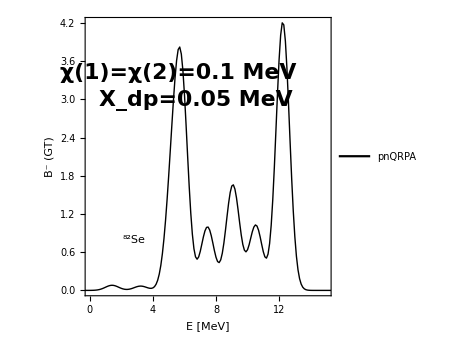

```mathematica
tableFig1=Table[{enBMSe[[i]],strBMSe[[i]]},{i,1,Length[strBMSe]}];
fig1=ListPlot[tableFig1,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{0,15},Full},FrameLabel->{"E [MeV]","B^- (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.4,0.9}],Epilog->{Inset[Style["χ(1)=χ(2)=0.1 MeV",22,Bold,Black,FontFamily->"Times"],Scaled[{0.38,0.8}]],Inset[Style["X_dp=0.05 MeV",22,Bold,Black,FontFamily->"Times"],Scaled[{0.45,0.7}]],Inset[Framed[Style[Row[{Superscript["","82"],"Se"}],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.2,0.2}]]}];
Show[fig1]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_3/new_figs/fig1_set3.pdf",Show[fig1],ImageResolution->1200];
```

## Figure 2

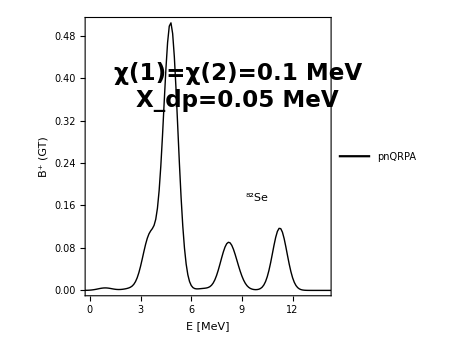

```mathematica
tableFig2=Table[{enBPSe[[i]],strBPSe[[i]]*1000},{i,1,Length[strBPSe]}];
fig2=ListPlot[tableFig2,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{0,14},Full},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.6,0.9}],Epilog->{Inset[Style["χ(1)=χ(2)=0.1 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.62,0.8}]],Inset[Style["X_dp=0.05 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.62,0.7}]],Inset[Framed[Style[Row[{Superscript["","82"],"Se"}],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.7,0.35}]]}];
Show[fig2]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_3/new_figs/fig2_set3.pdf",Show[fig2],ImageResolution->1200];
```

## Figure 3

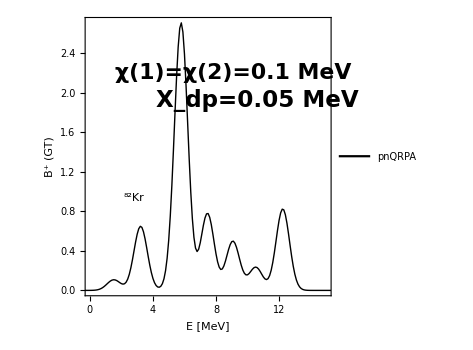

```mathematica
tableFig3=Table[{enBPKr[[i]],strBPKr[[i]]*1000},{i,1,Length[strBPKr]}];
fig3=ListPlot[tableFig3,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{0,15},Full},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.68,0.9}],Epilog->{Inset[Style["χ(1)=χ(2)=0.1 MeV",22,Bold,Black,FontFamily->"Times"],Scaled[{0.6,0.8}]],Inset[Style["X_dp=0.05 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.7,0.7}]],Inset[Framed[Style[Row[{Superscript["","82"],"Kr"}],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.2,0.35}]]},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}}];
Show[fig3]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_3/new_figs/fig3_set3.pdf",Show[fig3],ImageResolution->1200];
```